```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
descdat=ReadList[StringJoin[descDir,seperator,"desc.dat"],{Word,Word,Word,Number,Number,Number,Number,Word}];
Print["CleanCounts: Runs in the list, runNum = ",runnum=descdat[[{-26},4]]]
Print["CleanCounts: Runs in the list, dimNum = ",dimNum=Dimensions[runnum][[1]]];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

CleanCounts: Runs in the list, runNum = {13099}

CleanCounts: Runs in the list, dimNum = 1

```mathematica
excllmt1=.35;(*.1**************************************)
excllmt=.0485;(*.0485**************************************)
Monitor[
For[runi=1,runi≤dimNum,runi++,
runNum=runnum[[runi]];
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
data=ReadList[StringJoin[AscDir,seperator,IntegerString[runNum,10,6],seperator,IntegerString[runNum,10,6],"_Meta5.edm"],metaStructure2];
begCy=1;
maxCy=Dimensions[data][[1]];
ptud=Table[{data[[k]][[2]],{data[[k]][[27]]+data[[k]][[28]],Sqrt[data[[k]][[27]]+data[[k]][[28]]]}/1000},{k,begCy,maxCy}];
ptmon=Table[{data[[k]][[2]],{data[[k]][[30]],Sqrt[data[[k]][[30]]]}/10000},{k,begCy,maxCy}];
ptudmon=Table[{data[[k]][[2]],{(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]],((Sqrt[data[[k]][[27]]+data[[k]][[28]]])/data[[k]][[30]]+(Sqrt[data[[k]][[30]]]*(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]^2))}},{k,begCy,maxCy}];
ftudmon=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]},{k,begCy,maxCy}];
errudmon=Table[ptudmon[[k]][[2]][[2]],{k,begCy,maxCy}];
nlmudmon=NonlinearModelFit[ftudmon,aa,{{aa,1}},xx];
pt1=EDAListPlot[ptud,PlotRange->{{begCy,maxCy},{0,120}},ImagePadding->125,PlotStyle->{Blue},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}];
pt2=EDAListPlot[ptmon,PlotRange->{{begCy,maxCy},{0,120}},ImagePadding->125,PlotStyle->{Red},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}];
pt3=Overlay[{pt1,pt2},ImageSize->1200];
ptudmonres=Table[{k-1+begCy,nlmudmon["FitResiduals"][[k]]},{k,1,maxCy-begCy+1}];
sdptudmonres=StandardDeviation[ptudmonres[[;;,2]]];
avgptudmonres=Mean[ftudmon[[;;,2]]];
pt4=Show[{
Plot[{nlmudmon[x]+sdptudmonres,nlmudmon[x]-sdptudmonres,
nlmudmon[x]+2sdptudmonres,nlmudmon[x]-2sdptudmonres,
nlmudmon[x]+3sdptudmonres,nlmudmon[x]-3sdptudmonres
nlmudmon[x]},{x,begCy,maxCy},Filling->{{1->{2}},{3->{4}},{5->{6}}},PlotRange->{{begCy,maxCy},{avgptudmonres-3sdptudmonres,avgptudmonres+3sdptudmonres}},PlotStyle->{None,None,None,None,None,None,{Red,Thick}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n=(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1400}],
EDAListPlot[ptudmon,PlotRange->{{begCy,maxCy},{-3sdptudmonres,3sdptudmonres}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n=(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200},PlotMarkers->{Blue, Medium}]
},ImagePadding->185];
pt5=Show[{
Plot[{sdptudmonres,-sdptudmonres,
2sdptudmonres,-2sdptudmonres,
3sdptudmonres,-3sdptudmonres
},{x,begCy,maxCy},Filling->{{1->{2}},{3->{4}},{5->{6}},{7->{8}},{9->{10}}},PlotRange->{{begCy,maxCy},{-3sdptudmonres,3sdptudmonres}},PlotStyle->None,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n-Residual"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1400}],
EDAListPlot[ptudmonres,PlotRange->{{begCy,maxCy},{-.005,.005}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n-Residual"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1400},PlotMarkers->{Red, Medium}]
},ImagePadding->185];
pt6=GraphicsGrid[{{pt4,pt5}}];
cntint={};
For[i=begCy+2,i≤maxCy-2,i++,
If[(
(
Abs[nlmudmon["FitResiduals"][[i-begCy+1]]]>4sdptudmonres
)||
(
data[[i]][[30]]<500000;
)||
(
(data[[i]][[27]]+data[[i]][[28]])<5000;
)||
(
(
(Abs[data[[i]][[30]]-data[[i-2]][[30]]]>excllmt1*data[[i]][[30]])&&
(Abs[data[[i+2]][[30]]-data[[i]][[30]]]>excllmt1*data[[i]][[30]])
)&&
(
(Abs[data[[i]][[30]]-data[[i-1]][[30]]]>excllmt1*data[[i]][[30]])&&
(Abs[data[[i+1]][[30]]-data[[i]][[30]]]>excllmt1*data[[i]][[30]])
)
)||
(
Abs[ftudmon[[i]][[2]]-Mean[ftudmon[[;;,2]]]]>excllmt1*Mean[ftudmon[[;;,2]]]
)||
(
(
(Abs[ftudmon[[i]][[2]]-ftudmon[[i-2]][[2]]]>excllmt1*ftudmon[[i]][[2]])&&
(Abs[ftudmon[[i]][[2]]-ftudmon[[i+2]][[2]]]>excllmt1*ftudmon[[i]][[2]])
)&&
(
(Abs[ftudmon[[i]][[2]]-ftudmon[[i-1]][[2]]]>excllmt1*ftudmon[[i]][[2]])&&
(Abs[ftudmon[[i]][[2]]-ftudmon[[i+1]][[2]]]>excllmt1*ftudmon[[i]][[2]])
)
)
),
cntint=AppendTo[cntint,i];
];
];
bddataint=Part[data,cntint];
gddataint=DeleteCases[data,Alternatives@@bddataint];
maxCy2int=begCy+Dimensions[gddataint][[1]]-1;
(*Round 2*)
ftudmon2=Table[{gddataint[[k]][[2]],(gddataint[[k]][[27]]+gddataint[[k]][[28]])/gddataint[[k]][[30]]},{k,begCy,maxCy2int}];
nlmudmon2=NonlinearModelFit[ftudmon2,aa,{{aa,1}},xx];
ptudmonres2=Table[{k-1+begCy,nlmudmon2["FitResiduals"][[k]]},{k,1,maxCy2int-begCy+1}];
sdptudmonres2=StandardDeviation[ptudmonres2[[;;,2]]];
avgptudmonres2=Mean[ftudmon2[[;;,2]]];
cnt={};
For[i=begCy+2,i≤maxCy2int-2,i++,
If[(
(
Abs[nlmudmon2["FitResiduals"][[i-begCy+1]]]>4sdptudmonres2
)||
(
gddataint[[i]][[30]]<500000;
)||
(
(gddataint[[i]][[27]]+gddataint[[i]][[28]])<5000;
)||
(
(
(Abs[gddataint[[i]][[30]]-gddataint[[i-2]][[30]]]>excllmt*gddataint[[i-2]][[30]])&&
(Abs[gddataint[[i+2]][[30]]-gddataint[[i]][[30]]]>excllmt*gddataint[[i+2]][[30]])
)&&
(
(Abs[gddataint[[i]][[30]]-gddataint[[i-1]][[30]]]>excllmt*gddataint[[i-1]][[30]])&&
(Abs[gddataint[[i+1]][[30]]-gddataint[[i]][[30]]]>excllmt*gddataint[[i+1]][[30]])
)
)||
(
Abs[ftudmon2[[i]][[2]]-Mean[ftudmon2[[;;,2]]]]>excllmt*Mean[ftudmon2[[;;,2]]]
)||
(
(
(Abs[ftudmon2[[i]][[2]]-ftudmon2[[i-2]][[2]]]>excllmt*ftudmon2[[i-2]][[2]])&&
(Abs[ftudmon2[[i]][[2]]-ftudmon2[[i+2]][[2]]]>excllmt*ftudmon2[[i+2]][[2]])
)&&
(
(Abs[ftudmon2[[i]][[2]]-ftudmon2[[i-1]][[2]]]>excllmt*ftudmon2[[i-1]][[2]])&&
(Abs[ftudmon2[[i]][[2]]-ftudmon2[[i+1]][[2]]]>excllmt*ftudmon2[[i+1]][[2]])
)
)
),
cnt=AppendTo[cnt,i];
];
];
bddata=Part[gddataint,cnt];
gddata=DeleteCases[gddataint,Alternatives@@bddata];
maxCy2=begCy+Dimensions[gddata][[1]]-1;
(**)
gdptud=Table[{gddata[[k]][[2]],{gddata[[k]][[27]]+gddata[[k]][[28]],Sqrt[gddata[[k]][[27]]+gddata[[k]][[28]]]}/1000},{k,begCy,maxCy2}];
gdptmon=Table[{gddata[[k]][[2]],{gddata[[k]][[30]],Sqrt[gddata[[k]][[30]]]}/10000},{k,begCy,maxCy2}];
gdptudmon=Table[{gddata[[k]][[2]],{(gddata[[k]][[27]]+gddata[[k]][[28]])/gddata[[k]][[30]],.002+((Sqrt[gddata[[k]][[27]]+gddata[[k]][[28]]])/gddata[[k]][[30]]+(Sqrt[gddata[[k]][[30]]]*(gddata[[k]][[27]]+gddata[[k]][[28]])/gddata[[k]][[30]]^2))}},{k,begCy,maxCy2}];
gdftudmon=Table[{gddata[[k]][[2]],(gddata[[k]][[27]]+gddata[[k]][[28]])/gddata[[k]][[30]]},{k,begCy,maxCy2}];
gderrudmon=Table[gdptudmon[[k]][[2]][[2]],{k,begCy,maxCy2}];
gdpt1=EDAListPlot[gdptud,PlotRange->{{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},{0,120}},ImagePadding->125,PlotStyle->{Blue},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}];
gdpt2=EDAListPlot[gdptmon,PlotRange->{{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},{0,120}},ImagePadding->125,PlotStyle->{Red},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}];
gdpt3=Overlay[{gdpt1,gdpt2},ImageSize->1200];
gdnlmudmon=NonlinearModelFit[gdftudmon,aa,{{aa,1}},xx];
gdptudmonres=Table[{k-1+begCy,gdnlmudmon["FitResiduals"][[k]]},{k,1,maxCy2-begCy+1}];
sdgdptudmonres=StandardDeviation[gdptudmonres[[;;,2]]];
avggdptudmon=Mean[gdftudmon[[;;,2]]];
gdpt4=Show[{
Plot[{
gdnlmudmon[x]+sdgdptudmonres,gdnlmudmon[x]-sdgdptudmonres,
gdnlmudmon[x]+2sdgdptudmonres,gdnlmudmon[x]-2sdgdptudmonres,
gdnlmudmon[x]+3sdgdptudmonres,gdnlmudmon[x]-3sdgdptudmonres
,gdnlmudmon[x]},{x,gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},Filling->{{1->{2}},{3->{4}},{5->{6}}},PlotRange->{{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},{avggdptudmon-3sdgdptudmonres,avggdptudmon+3sdgdptudmonres}},PlotStyle->{None,None,None,None,None,None,{Red,Thick}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n=(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1400}],
EDAListPlot[gdptudmon,PlotRange->{{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},{avgptudmonres2-3sdgdptudmonres,avgptudmonres2+3sdgdptudmonres}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n=(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1400},PlotMarkers->{Blue, Medium}]
},ImagePadding->185];
gdpt5=Show[{
Plot[{sdgdptudmonres,-sdgdptudmonres,
2sdgdptudmonres,-2sdgdptudmonres,
3sdgdptudmonres,-3sdgdptudmonres
},{x,begCy,maxCy2},Filling->{{1->{2}},{3->{4}},{5->{6}},{7->{8}},{9->{10}}},Filling->{{1->{2}},{3->{4}},{5->{6}}},PlotRange->{{begCy,maxCy2},{-3sdgdptudmonres,3sdgdptudmonres}},PlotStyle->None,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n-Residual"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1400}],
EDAListPlot[gdptudmonres,PlotRange->{{gddata[[begCy]][[2]],gddata[[maxCy2]][[2]]},{-3sdgdptudmonres,3sdgdptudmonres}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n-Residual"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1400},PlotMarkers->{Red, Medium}]
},ImagePadding->185];
gdpt6=GraphicsGrid[{{gdpt4,gdpt5}}];
Export[StringJoin[AscDir,seperator,IntegerString[runNum,10,6],seperator,IntegerString[runNum,10,6],"_info.dat"],{maxCy,maxCy2int,maxCy2,"\n"}];
Export[StringJoin[AscDir,seperator,IntegerString[runNum,10,6],seperator,IntegerString[runNum,10,6],"_Meta5-2.dat"],gddata];
Export[StringJoin[PicDir,seperator,IntegerString[runNum,10,6],"_pureUD-Mon.png"],pt3];
Export[StringJoin[PicDir,seperator,IntegerString[runNum,10,6],"_pureUDMon.png"],pt6];
Export[StringJoin[PicDir,seperator,IntegerString[runNum,10,6],"_cutUD-Mon.png"],gdpt3];
Export[StringJoin[PicDir,seperator,IntegerString[runNum,10,6],"_cutUDMon.png"],gdpt6];
];,ProgressIndicator[runi/dimNum,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
```

```mathematica
descdat[[;;,4]]
```

{12693,12695,12697,12704,12707,12770,12771,12772,12773,12774,12775,12778,12779,12780,12781,13099,13101,13102,13103,13104,13105,13106,13107,13108,13109,13110,13111,13112,13132,13133,13134,13135,13136,13137,13138,13139,13140,13141,13142,13145}

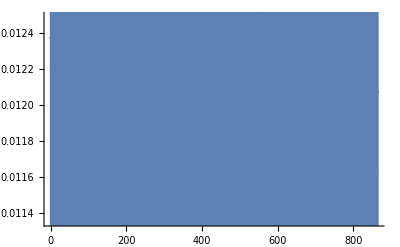

```mathematica
EDAListPlot[gdptudmon]
```